```mathematica
Definindo parâmetros geométricos
```

Definindo geométricos parâmetros

```mathematica
x=.;y=.;r=.; 
L=100;
psi = Pi/1.1;
a= 5;
b = 5;
c= 5;
r[x_,y_]:={((L/(2psi) )+a  Cos[y])Cos[x], ((L/(2psi) )+b Cos[y] )Sin[x], c Sin[y]};
```

```mathematica
gr2=ParametricPlot3D[r[x,y],{x,0,2psi},{y,0,2Pi},Boxed->False];
Show[gr2]
```

-Graphics3D-

```mathematica
Clear["Global`*"]
x=.;y=.;r=.; 
L=1000 10^(-9);
psi = Pi/1.1;
a= 50   10^(-9);
b = 50   10^(-9);
c= 50  10^(-9);


rc={((L/(2psi) )+a  Cos[y])Cos[x], ((L/(2psi) )+b Cos[y] )Sin[x], c Sin[y]};
rp[x_,y_]={((L/(2psi) )+a  Cos[y])Cos[x], ((L/(2psi) )+b Cos[y] )Sin[x], c Sin[y]};
gx[x_,y_]=Simplify[D[rp[x,y],x]];
gy[x_,y_]=Simplify[D[rp[x,y],y]];

gxx[x_,y_]:=gx[x,y].gx[x,y];
hx[x_,y_]:=Sqrt[gxx[x,y]];

gyy[x_,y_]:=gy[x,y].gy[x,y];
hy[x_,y_]:=Sqrt[gyy[x,y]];

g1[α_]:=D[rc,α];
g[α_,β_]:=g1[α].g1[β];
h1[α_]:=Sqrt[g[α,α]];
e1[α_]:=g1[α]/h1[α];
n=Cross[e1[y],e1[x]];
bt[α_,β_]:=n.D[g1[α],β];
h[α_,β_]:=bt[α,β]/(h1[α]h1[β]);
G=h[x,x]h[y,y];
M=(h[x,x]+h[y,y])/2;

Gr[α_]:=e1[x](1/h1[x])D[α,x]+e1[y](1/h1[y])D[α,y];
ω[α_]:=e1[y].D[e1[x],α];
Ω={ω[y]/h1[y],ω[x]/h1[x],0};
```

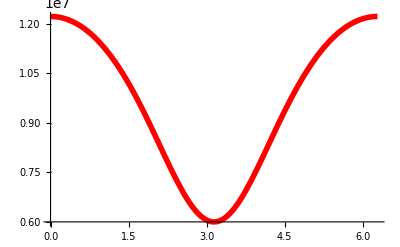

```mathematica
x=0;
Plot[M,{y,0,2 Pi},TicksStyle->Directive[Bold,20],PlotStyle->Directive[Thickness[0.01],Red] (*Cambia el color a rojo*)]
```

```mathematica
r0=.;
x=.;
y=.;
x0 = 0;
y0=0;
thick= 10 10^(-9);
Ku1=2 10^5;
mu0=4π 10^(-7);
Ms=1.1 10^5;
DM = 1.1 10^{-3};
Aex=8.78 10^(-12);
Lex=Sqrt[(2 Aex)/(mu0 (Ms)^2)];
Q = (2Ku1)/(mu0 (Ms)^2);
Xi = Sqrt[Q-1];
R = 8 10^(-9);

Φ[y0_]:=-ArcTan[h1[x](x-x0),h1[y](y-y0)];
Θ[y0_]:=2ArcTan[((R)Exp[(Xi/Lex)(R - Sqrt[(hx[x,y](x-x0))^2+(hy[x,y](y-y0))^2])])/(Sqrt[(hx[x,y](x-x0))^2+(hy[x,y](y-y0))^2])]
Θ2[x_,y_]:=2ArcTan[((R)Exp[(Xi/Lex)(R - Sqrt[(hx[x,y](x-x0))^2+(hy[x,y](y-y0))^2])])/(Sqrt[(hx[x,y](x-x0))^2+(hy[x,y](y-y0))^2])]

r0Values=Table[r0,{r0,Pi/2,3Pi/2,Pi/8}];

Γ[y0_]:={h[x,x]Cos[Φ[y0]]+h[x,y]Sin[Φ[y0]],h[y,x]Cos[Φ[y0]]+h[y,y]Sin[Φ[y0]],0};

DΓ[y0_]:={-h[x,x]Sin[Φ[y0]]+h[x,y]Cos[Φ[y0]],-h[y,x]Sin[Φ[y0]]+h[y,y]Cos[Φ[y0]],0};
```

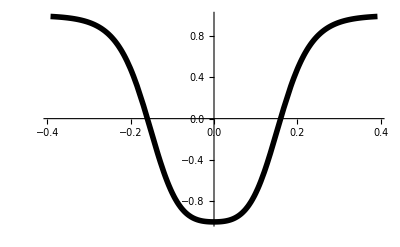

```mathematica
Plot[Cos[Θ2[0,y]],{y,-Pi/8,Pi/8},PlotRange->Full,TicksStyle->Directive[Bold,20],PlotStyle->Directive[Thickness[0.01],Black]]
```

1.41187×10^-17

OpenWrite::noopen: Cannot open C:\Users\josec\OneDrive\Documentos\troca_results3.csv.

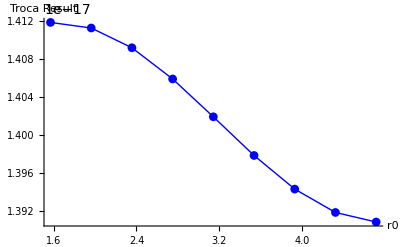

```mathematica
ϵTroca[y0_]:=Aex((Gr[Θ[y0]]-Γ[y0]).(Gr[Θ[y0]]-Γ[y0])+(Sin[Θ[y0]](Gr[Φ[y0]]-Ω)-Cos[Θ[y0]]DΓ[y0]).(Sin[Θ[y0]](Gr[Φ[y0]]-Ω)-Cos[Θ[y0]]DΓ[y0]));


trocaint= NIntegrate[thick*ϵTroca[Pi/2]*(h1[x]*h1[y]),{y, 0,2Pi},{x,0,2psi}]

trocaResults=Table[NIntegrate[thick*ϵTroca[r0]*(h1[x]*h1[y]),{y, 0,2Pi},{x,0,2psi}],{r0,r0Values}];
dataForPlottroca=Transpose[{r0Values,trocaResults}];
Export["troca_results3.csv",dataForPlottroca,"CSV"];
ListPlot[dataForPlottroca,AxesLabel->{"r0","Troca Result"},PlotMarkers->Automatic,Joined->True,PlotStyle->Directive[Blue,Thick]]
```

3.86047×10^-19

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

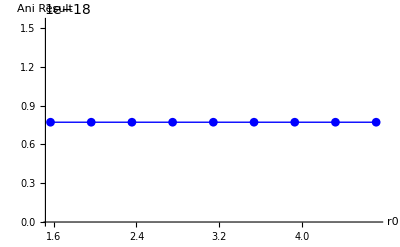

```mathematica
ϵAni[y0_]:=(Ku1-(mu0 Ms^2)/2) (1-Cos[Θ[y0]]^2);
aniint= NIntegrate[thick*ϵAni[0]*(h1[x]*h1[y]),{y,0,2Pi},{x,0,2psi}]

aniResults=Table[NIntegrate[thick*ϵAni[r0]*(h1[x]*h1[y]),{y,0,4Pi},{x,0,2psi}],{r0,r0Values}];
dataForPlotani=Transpose[{r0Values,aniResults}];
ListPlot[dataForPlotani,AxesLabel->{"r0","Ani Result"},PlotMarkers->Automatic,Joined->True,PlotStyle->Directive[Blue,Thick]]
```

```mathematica
VectA[y0_]:= 2 Gr[Θ[y0]]-Γ[y0];
VectB[y0_]:={Cos[Φ[y0]],Sin[Φ[y0]],0};

ϵDMI[y0_]:=DM(Sin[Θ[y0]]*Sin[Θ[y0]]*((2 Gr[Θ[y0]]-Γ[y0]).(n)));dmiint= NIntegrate[thick*ϵDMI[Pi/2]*(h1[x]*h1[y]),{y,0,2Pi},{x,0,2psi}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

{0.}

```mathematica
tResults=Table[NIntegrate[thick*(ϵAni[r0]+ϵTroca[r0]+ϵDMI[r0])*(h1[x]*h1[y]),{y,-Pi,Pi},{x,-psi,psi}],{r0,r0Values}];
dataForPlott=Transpose[{r0Values,tResults}];
ListPlot[dataForPlott,AxesLabel->{"r0","Total Result"},PlotMarkers->Automatic,Joined->True,PlotStyle->Directive[Blue,Thick]]
```

{1.56722×10^-17}

```mathematica
Chop[tint]
```

{0}